```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching ""Global`*"".

```mathematica
D[A*x^n,x ]
```

A n x^(-1+n)

```mathematica
polynomial = A*x^n + B*y^m
```

A x^n+B y^m

```mathematica
D[polynomial, x]
```

A n x^(-1+n)

```mathematica
D[polynomial, A]
```

x^n

```mathematica
D[polynomial, y]
```

B m y^(-1+m)

```mathematica
D[polynomial, x, x]
D[polynomial, {x,2}]
```

A (-1+n) n x^(-2+n)

A (-1+n) n x^(-2+n)

```mathematica
D[polynomial, {x,0}]
```

A x^n+B y^m

```mathematica
D[polynomial, x]D[polynomial, y]
```

A B m n x^(-1+n) y^(-1+m)

```mathematica
D[polynomial, x, y]
```

0

```mathematica
f[var_] = Sqrt[var];f'[x]
```

1/(2 √x)

```mathematica
Integrate[polynomial, x, y]
```

x y ((A x^n)/(1+n)+(B y^m)/(1+m))

```mathematica
Integrate[A/x, x]
```

A Log[x]

```mathematica
Integrate[A*x^n, {x,0,2}]
```

ConditionalExpression[(2^(1+n) A)/(1+n),Re[n]>-1]

```mathematica
Integrate[A*x^n,{x,0,2}, Assumptions ->n>0]
```

(2^(1+n) A)/(1+n)

```mathematica
Assuming[n>0, Integrate[A*x^n, {x,0,2}]]
```

(2^(1+n) A)/(1+n)

```mathematica
Integrate[Exp[-x^2],x]
```

1/2 √π Erf[x]

```mathematica
Integrate[Exp[-x^2],{x,0,Infinity}]
```

(√π)/2

```mathematica
force = -k*x; Omega = Sqrt[k/m]; xMass = A*Cos[Omega*t];
```

```mathematica
work = Integrate[force, {x,A,0}]
```

(A^2 k)/2

```mathematica
vel = D[xMass, t]
```

-A √(k/m) Sin[√(k/m) t]

```mathematica
vmax = vel/.{t->Pi/(2*Omega)}
```

-A √(k/m)

```mathematica
deltaKE = (1./2.)*m*vmax^2
```

0.5 A^2 k

```mathematica
Integrate[2/√Pi Exp[-x^2], {x,0,∞}]
```

1

```mathematica
NIntegrate[2/√Pi Exp[-x^2], {x,0,0.1}]
```

0.112463

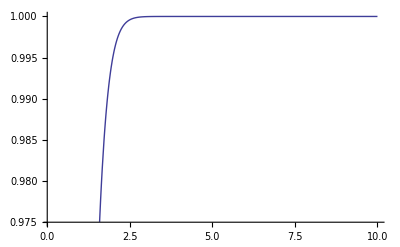

```mathematica
Plot[NIntegrate[2/√Pi Exp[-x^2], {x,0,x0}],{x0,0.1,10}]
```

```mathematica
NIntegrate[1/√(1+x+x^3),{x,0,1}]
```

0.784573